## Постановка задачи

## Законы Ньютона

```mathematica
k=.;
Eq1:=m a == - k v + F+m ({{0}, {-g}});
NF[t_]=m f[t];
a=( {{vx'[t]}, {vy'[t]}});
v=({{vx[t]}, {vy[t]}});
F=NF[t]({{Cos[α[t]]}, {Sin[α[t]]}});
Eq2=Eq1
v=.;a=.;F=.;
Eq2/.{vx->Subscript[v, x],vy->Subscript[v, y],F0->Subscript[F, 0],t0->Subscript[t, 0]}//TraditionalForm
```

{{m vx'[t]},{m vy'[t]}}=={{m Cos[α[t]] f[t]-k vx[t]},{-g m+m f[t] Sin[α[t]]-k vy[t]}}

(m v_x'(t)
m v_y'(t))==(m cos(α(t)) f(t)-k v_x(t)
-g m+f(t) sin(α(t)) m-k v_y(t))

```mathematica
Cond1:=-π/2≤α[t]≤π/2;
```

## Решение уравнений

```mathematica
DSolve[{Eq2, vy[0]==0, vx[0]==0}, {vx[t],vy[t]}, t]//Simplify
```

{{vx[t]→ⅇ^(-(k t)/m) (-∫_1^0 ⅇ^((k K[1])/m) Cos[α[K[1]]] f[K[1]]ⅆK[1]+∫_1^t ⅇ^((k K[1])/m) Cos[α[K[1]]] f[K[1]]ⅆK[1]),vy[t]→ⅇ^(-(k t)/m) (-∫_1^0 ⅇ^((k K[2])/m) (-g+f[K[2]] Sin[α[K[2]]])ⅆK[2]+∫_1^t ⅇ^((k K[2])/m) (-g+f[K[2]] Sin[α[K[2]]])ⅆK[2])}}

```mathematica
k=.;
vx[t_]=ⅇ^(-(k t)/m)∫_0^t ⅇ^((k t2)/m) f[t] Cos[α[t2]]ⅆt2;
vy[t_]=ⅇ^(-(k t)/m)∫_0^t ⅇ^((k t2)/m) (-g + f[t] Sin[α[t2]])ⅆt2;
```

## Длина пути

```mathematica
L=∫_0^t1 vx[t]ⅆt;
```

## Уравнения на t1

```mathematica
MainEq1:=0==∫_0^t1 vy[t]ⅆt
```

## Простой случай

```mathematica
k=0;
vx[t]
vy[t]//FullSimplify
```

∫_0^t Cos[α[t2]] f[t]ⅆt2

∫_0^t (-g+f[t] Sin[α[t2]])ⅆt2

## Уравнение связи ускорений

```mathematica
Clear[vx];
Clear[vy];
Clear[ax];
ax=.; ay=.;
ax->vx'[t];
ay->vy'[t];
ax^2+(ay+g)^2==f[t]^2
```

ax^2+(ay+g)^2==f[t]^2

## Решение уравнения

```mathematica
ax[t_]=√(f[t]^2-(ay[t]+g)^2);
```

## Вариационная задача 1

```mathematica
L=∫_0^t1 (∫_0^t2 √(f[t]^2-(vy'[t]+g)^2)ⅆt)ⅆt2
∫_0^t1 vy[t]ⅆt==0
```

## Вариационная задача 2

```mathematica
L=∫_0^t1 (∫_0^t2 √(f[t]^2-(ay[t]+g)^2)ⅆt)ⅆt2
∫_0^t1 (∫_0^t2 ay[t]ⅆt)ⅆt==0
```

## Решение 2 задачи

```mathematica
Clear[ay]
D[√(f[t]^2-(ay+g)^2)+λ ay,ay]==0
Sol1 = Solve[%,ay][[2]][[1]]
```

λ-(ay+g)/(√(-(ay+g)^2+f[t]^2))==0

ay→(-g-g λ^2+√(λ^2 f[t]^2+λ^4 f[t]^2))/(1+λ^2)

```mathematica
ax[t]/.{ay[t]->ay}/.Sol1//Simplify
```

√(f[t]^2/(1+λ^2))

Получается, что без трения необходимо тянуть под постоянным углом

## Решение 1 задачи

## Случай с трением

## Уравнение связи ускорений

```mathematica
Clear[vx];
Clear[vy];
Clear[ax];
Clear[f];
ax=.; ay=.;
Ch:={ax->vx'[t],
ay->vy'[t],
vx->vx[t],
vy->vy[t]};
(ax+β vx)^2+(ay+g+β vy)^2==f[t]^2
```

(ax+vx β)^2+(ay+g+vy β)^2==f[t]^2

```mathematica
ax == √(f[t]^2-(ay+g+β vy)^2)- β vx
DSolve[%/.Ch,vx[t],t]
```

ax==-vx β+√(-(ay+g+vy β)^2+f[t]^2)

{{vx[t]→ⅇ^(-t β) C[1]+ⅇ^(-t β) ∫_1^t ⅇ^(β K[1]) √(f[K[1]]^2-(g+β vy[K[1]]+vy'[K[1]])^2)ⅆK[1]}}

```mathematica
vx[t_]=ⅇ^(-t β) ∫_0^t ⅇ^(t2 β) √(f[t2]^2-(g+β vy[t2]+vy'[t2])^2)ⅆt2
```

ⅇ^(-t β) ∫_0^t ⅇ^(t2 β) √(f[t2]^2-(g+β vy[t2]+vy'[t2])^2)ⅆt2

## Вариационная задача 1

```mathematica
Clear[vy];L=.;
L==∫_0^t1 (ⅇ^(-t β) ∫_0^t ⅇ^(t2 β) √(f[t2]^2-(g+β vy[t2]+vy'[t2])^2)ⅆt2)ⅆt;
∫_0^t1 (∫_0^t vy'[t2]ⅆt2)ⅆt==0;
```

```mathematica
F[t2_,t_,vy_,vyd_]=ⅇ^((t - t2) β)√(f[t]^2-(g+β vy+vyd)^2)+λ vyd
```

vyd λ+ⅇ^((t-t2) β) √(-(g+vyd+vy β)^2+f[t]^2)

## Уравнение Лагранжа-Эйлера

```mathematica
z:={vy->vy[t],vyd->vy'[t]}
((D[F[t2,t,vy,vyd], vy])/.z)-D[((D[F[t2,t,vy,vyd], vyd])/.z), t]==0//FullSimplify
DEq1=FullSimplify[%,Assumptions->{√(f[t]^2-(g+β vy[t]+vy'[t])^2)≠0,f[t]≠0}]
```

(f[t] (-f'[t] (g+β vy[t]+vy'[t])+f[t] (β vy'[t]+vy''[t])))/(√(f[t]^2-(g+β vy[t]+vy'[t])^2))==0

f'[t] (g+β vy[t]+vy'[t])==f[t] (β vy'[t]+vy''[t])

Подставляем f[t]

```mathematica
Clear[vy]
f[t_]=f0/(1+t/t0)^2;
FullSimplify[DEq1,Assumptions->{t+t0≠0,f0≠0,t0≠0}]
vy[t_]=vy[t]/.DSolve[DEq1,vy[t],t][[1]][[1]]
```

2 g+2 β vy[t]+(2+(t+t0) β) vy'[t]+(t+t0) vy''[t]==0

-g/β+ⅇ^(-t β) C[1]+ⅇ^(-t β) C[2] (-ⅇ^((t+t0) β)/(t+t0)+β ExpIntegralEi[(t+t0) β])

### Общий случай

```mathematica
vy[t]
g+β vy[t]+vy'[t]//FullSimplify
```

-g/β+ⅇ^(-t β) C[1]+ⅇ^(-t β) C[2] (-ⅇ^((t+t0) β)/(t+t0)+β ExpIntegralEi[(t+t0) β])

(ⅇ^(t0 β) C[2])/(t+t0)^2

```mathematica
L==∫_0^t1 (ⅇ^(-t β) ∫_0^t ⅇ^(t2 β) √(f[t2]^2-(g+β vy[t2]+vy'[t2])^2)ⅆt2)ⅆt
```

$Aborted

Поиск C[1], C[0]

```mathematica
Solve[{∫_0^t1 vy[t]ⅆt==0,vy[0]==0},{C[1],C[2]}]//FullSimplify
```

$Aborted

```mathematica
Series[vy[t],{β,∞,0}]
```

-1/(t+t0)ⅇ^(-t β) (ⅇ^(t β+t0 β) C[2]+ⅇ^(t β) ((g t)/β+O[1/β]^2)+ⅇ^(t β) ((g t0)/β+O[1/β]^2)+ⅇ^(t β+t0 β) (-(t^3 C[2])/(t+t0)^3-(t^3 C[2])/((t+t0)^4 β)+O[1/β]^2)+ⅇ^(t β+t0 β) (-(2 (t^2 t0 C[2]))/(t+t0)^3-(2 (t^2 t0 C[2]))/((t+t0)^4 β)+O[1/β]^2)+ⅇ^(t β+t0 β) (-(t^2 t0 C[2])/(t+t0)^3-(t^2 t0 C[2])/((t+t0)^4 β)+O[1/β]^2)+ⅇ^(t β+t0 β) (-(2 (t t0^2 C[2]))/(t+t0)^3-(2 (t t0^2 C[2]))/((t+t0)^4 β)+O[1/β]^2)+ⅇ^(t β+t0 β) (-(t t0^2 C[2])/(t+t0)^3-(t t0^2 C[2])/((t+t0)^4 β)+O[1/β]^2)+ⅇ^(t β+t0 β) (-(t0^3 C[2])/(t+t0)^3-(t0^3 C[2])/((t+t0)^4 β)+O[1/β]^2)+((-1/2 t (-C[2] Log[-t-t0]+C[2] Log[-1/(t+t0)]-C[2] Log[1/(t+t0)]+C[2] Log[t+t0])-1/2 t0 (-C[2] Log[-t-t0]+C[2] Log[-1/(t+t0)]-C[2] Log[1/(t+t0)]+C[2] Log[t+t0])) β+(-t C[1]-t0 C[1])+O[1/β]^3))

### Приближение t0>>m/k

```mathematica
Clear[vy];
2 g+2 β vy[t]+(2+(t0) β) vy'[t]+(t0) vy''[t]==0;
vy[t_]=vy[t]/.DSolve[%,vy[t],t][[1]][[1]]
```

-g/β+ⅇ^(-t β) C[1]+ⅇ^(-(2 t)/t0) C[2]

### Приближение t0>>m/k (2)

```mathematica
Clear[vy]
f[t_]=f0/(1+t/t0)^2;
vx[t_]=Cos[α] f[t]/β;
vy[t_]=(Sin[α]f[t]-g)/β;
α0=ArcSin[g/f0];
```

```mathematica
$Assumptions={t0>0,t1>0};
∫_0^t1 vy[t]ⅆt==0
Sol2=Solve[{%,t1≠0},t1][[1]][[1]]
```

(t1 (-g+(f0 t0 Sin[α])/(t0+t1)))/β==0

t1→(-g t0+f0 t0 Sin[α])/g

t1 (-1+2/(1+t1))

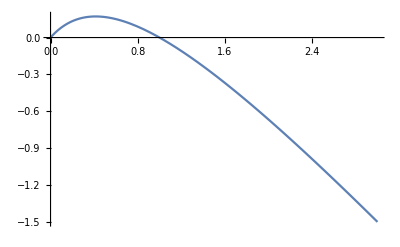

```mathematica
y[t1_]=∫_0^t1 vy[t]ⅆt/.{t0->1,f0->2,g->1,α->π/2,β->1}//FullSimplify
Plot[y[t],{t,0,3}]
```

```mathematica
Clear[L]
L[α_]=∫_0^t1 vx[t]ⅆt/.Sol2//FullSimplify//TrigExpand
```

(f0 t0 Cos[α])/β-(g t0 Cot[α])/β

```mathematica
Solve[L'[α]==0/.{Sin[α]->a,Csc[α]->1/a},a][[1]][[1]]
αMax=ArcSin[a]/.%
```

a→g^(1/3)/f0^(1/3)

ArcSin[g^(1/3)/f0^(1/3)]

```mathematica
L[αMax]//FullSimplify
```

(f0^(1/3) (f0^(2/3)-g^(2/3)) √(1-g^(2/3)/f0^(2/3)) t0)/β